Age Estimation VGG-16 Trained on IMDB-WIKI

Predict a person's age from an image of their face

### Basic usage

```mathematica
SetDirectory[NotebookDirectory[]]
CurrentDate[]
```

D:\04_Face-aging kids protection

Wed 9 Sep 2020 16:21:28GMT+2.

```mathematica
ImageList={Import["S01.webp"],Import["S02.jpg"],Import["S03.jpg"],Import["S04.jpg"],Import["S05.jpg"],Import["S06.jpg"],Import["S07.jpg"],Import["S08.jpg"],Import["S09.jpg"],
Import["S10.jpg"],Import["S11.jpg"],Import["S12.jpg"],Import["S13.jpg"],Import["S14.jpg"],Import["S15.jpg"],Import["S16.jpg"]}
```

```mathematica
Length[ImageList]
```

16

```mathematica
izbor=7
img=ImageList⟦izbor⟧
```

7

```mathematica
(* Export["Slika02.png",%,ImageResolution->270]
```

```mathematica
faces=FindFaces[img]
```

{Rectangle[{336.5,826.5},{482.5,1003.5}],Rectangle[{981.5,771.5},{1125.5,961.5}],Rectangle[{600.5,441.5},{736.5,603.5}],Rectangle[{1327.5,507.5},{1456.5,668.5}]}

```mathematica
NumberPersonsOnPhoto=% // Length (* Prebrojava broj osoba na slici *)
```

4

```mathematica
(* uklanja se višak lica koja su nepotrebna *)
"faces=Delete[faces,4]"
```

faces=Delete[faces,4]

```mathematica
faces
```

{Rectangle[{336.5,826.5},{482.5,1003.5}],Rectangle[{981.5,771.5},{1125.5,961.5}],Rectangle[{600.5,441.5},{736.5,603.5}],Rectangle[{1327.5,507.5},{1456.5,668.5}]}

Crop the photograph:

```mathematica
faceElements=ImageTrim[img,#]&/@faces
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Export["Slika02.png",%,ImageResolution->270]
```

### Resource retrieval

Guess the age of a person from the cropped image:

```mathematica
t1=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI Data"][faceElements]
```

{53,32,13,10}

This net is designed to work with cropped images of faces only. If the photograph is not a facial image, the results may be unexpected:

### Face elimination based on face’s age

```mathematica
facesA={0};
For[ii=1,ii≤Length[t1],ii++,
If[t1⟦ii⟧≤16,facesA=Append[facesA,faces⟦ii⟧]]]
facesA;
faces=DeleteCases[facesA,0]
```

{Rectangle[{600.5,441.5},{736.5,603.5}],Rectangle[{1327.5,507.5},{1456.5,668.5}]}

```mathematica
ImageTrim[img,#]&/@faces
```

{-Graphics-,-Graphics-}

```mathematica
(* Export["Slika01.png",%,ImageResolution->270]
```

```mathematica
mask=Graphics[
Map[Disk[RegionCentroid[##],Sqrt[Area[##]]/2]&,faces,{1}],PlotRange-> Transpose[{{0,0},ImageDimensions[img]}],ImageSize->ImageDimensions[img]];
```

```mathematica
img=ImageList⟦izbor⟧
```

```mathematica
FinalPhoto=ImageCompose[img,SetAlphaChannel[Blur[img,50],ColorNegate@mask]]
```

```mathematica
Export["Slika02.jpg",%,ImageResolution->270]
```

Slika02.jpg

### Resource retrieval

Get the pre-trained net:

```mathematica
NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI Data"]
```

NetChain[<>]

Obtain the probability distribution over all possible ages:

```mathematica
probabilities=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI Data"][faceElements,"Probabilities"];
```

```mathematica
(* Pronalaženje maksimalne verovatnoće po godinama po osobi *)
t2=Table[0,{ii,Length[t1]}];
k=0;
For[k=1,k≤Length[t2],k++,ii=1;
While[ii≤101,If[t2⟦k⟧≤Normal[probabilities⟦k⟧]⟦ii⟧⟦2⟧,t2⟦k⟧=Normal[probabilities⟦k⟧]⟦ii⟧⟦2⟧];
ii++]]
t2
```

{0.0493423,0.0401523,0.0793051,0.0698959}

Plot the probability distribution over possible ages:

```mathematica
ListPlot[probabilities
,PlotRange->All
,GridLines->{t1,t2}
,GridLinesStyle->Directive[Black, Dashed]
,PlotStyle->{AbsoluteThickness[2]}
,Joined->True
,InterpolationOrder->3
,Frame->True
,ImageSize->600
,RotateLabel->True
,FrameStyle->Directive[Black,18]
,FrameLabel->{{"Probability",""},{"Ages",""}}
,FrameTicks->Automatic
,LabelStyle->Directive[Medium,Italic]
,PlotLegends->Placed[LineLegend[Table[faceElements⟦ii⟧,{ii,Length[faceElements]}],LegendFunction->None],{0.8,0.55}]
,Epilog->{PointSize[0.02],Black,Point[Table[{t1⟦ii⟧,t2⟦ii⟧},{ii,Length[t1]}]]}]
```

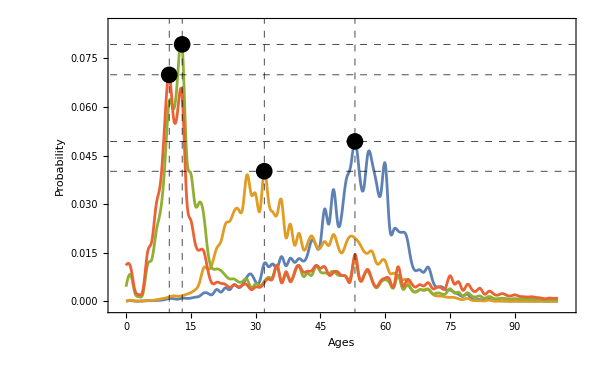

```mathematica
Export["Slika09Graph.jpg",-Graphics-,ImageResolution->270]
```

Slika09Graph.jpg

The recommended estimator of the age is the mean of the probability mass function:

```mathematica
AgeYears=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI Data"][faceElements,{"TopProbabilities",5}]
```

{{52→0.0416396,60→0.0425191,57→0.0427143,56→0.0457017,53→0.0493423},{36→0.0311801,29→0.0329518,30→0.0331429,28→0.0390364,32→0.0401523},{14→0.0461131,11→0.0593345,10→0.0616503,12→0.0702962,13→0.0793051},{9→0.0557324,11→0.0565908,12→0.0592868,13→0.0633882,10→0.0698959}}

```mathematica
%  // Transpose// TableForm
```

52→0.0416396 | 36→0.0311801 | 14→0.0461131 | 9→0.0557324
60→0.0425191 | 29→0.0329518 | 11→0.0593345 | 11→0.0565908
57→0.0427143 | 30→0.0331429 | 10→0.0616503 | 12→0.0592868
56→0.0457017 | 28→0.0390364 | 12→0.0702962 | 13→0.0633882
53→0.0493423 | 32→0.0401523 | 13→0.0793051 | 10→0.0698959

Probably range of ages:

```mathematica
AgeRange=Table[AgeYears⟦jj⟧⟦ii⟧⟦1⟧,{jj,NumberPersonsOnPhoto},{ii,5}]
```

{{52,60,57,56,53},{36,29,30,28,32},{14,11,10,12,13},{9,11,12,13,10}}

```mathematica
Table[Print[faceElements⟦jj⟧," → range between ",Min[Table[AgeYears⟦jj⟧⟦ii⟧⟦1⟧,{ii,5}]]," and ",Max[Table[AgeYears⟦jj⟧⟦ii⟧⟦1⟧,{ii,5}]]," old"],{jj,NumberPersonsOnPhoto}]
```

-Graphics- → range between 52 and 60 old

-Graphics- → range between 28 and 36 old

-Graphics- → range between 10 and 14 old

-Graphics- → range between 9 and 13 old

{Null,Null,Null,Null}

```mathematica
(* Pronalaženje maksimalne verovatnoće po godinama po osobi *)
t2=Table[0,{ii,Length[t1]}];
k=0;
For[k=1,k≤Length[t2],k++,ii=1;
While[ii≤101,If[t2⟦k⟧≤Normal[probabilities⟦k⟧]⟦ii⟧⟦2⟧,t2⟦k⟧=Normal[probabilities⟦k⟧]⟦ii⟧⟦2⟧];
ii++]]
t2
```

{0.0493423,0.0401523,0.0793051,0.0698959}

```mathematica
img
```

-Graphics-

```mathematica
FinalPhoto
```

-Graphics-